# Função Gama:

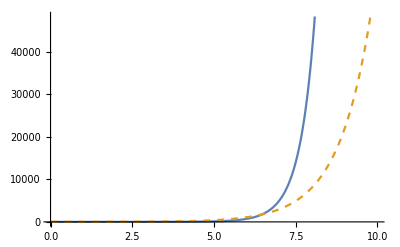

```mathematica
Plot[{Gamma[x+1],ⅇ^(x+1)},{x,0,10},PlotStyle->{Automatic,Dashed}]
```

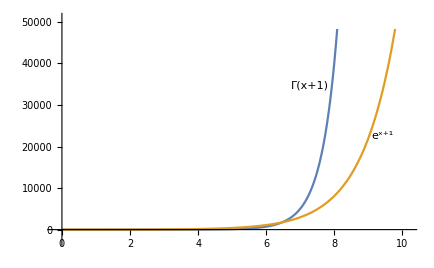

```mathematica
hm[z_,m_]:=Sum[BernoulliB[2n]/(2n*(2n-1))*1/(z^(2n-1)),{n,m}]
```

```mathematica
sm[z_,m_]:=Series[ⅇ^(hm[z,m]),{z,∞,2m-1}]
```

```mathematica
Do[Clear[z];Sn[p]=√(2π)z^(z+1/2)ⅇ^(-z)*N[Normal[sm[z,p]],30];,{p,1,61}]
```

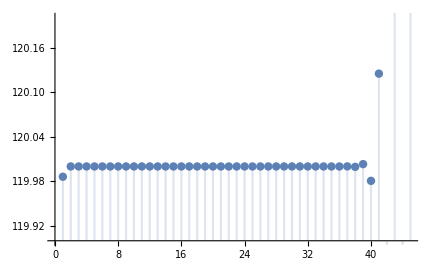

```mathematica
z=5;DiscretePlot[Sn[n],{n,1,45},PlotRange->{119.9,120.2}]
```

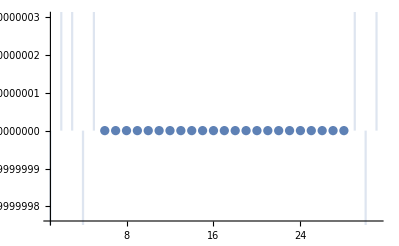

```mathematica
z=5;DiscretePlot[Sn[n],{n,1,31}]
```

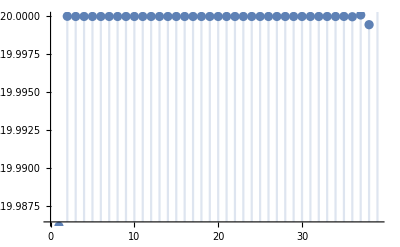

```mathematica
z=5;DiscretePlot[Sn[n],{n,1,39},PlotRange->{119.9864512,120.0000001}]
```

```mathematica
Gamma[6]
```

120

```mathematica
NumberForm[N[Sn[2]],26]
```

120.0000140573178

```mathematica
NumberForm[N[Sn[11]],26]
```

120.000000000001

```mathematica
NumberForm[N[Sn[26]],26]
```

119.999999999964

```mathematica
NumberForm[N[Sn[1]],26]
```

119.9861540902166

```mathematica
NumberForm[N[Sn[29]],26]
```

120.0000000009289

# Integrais de Fresnel:

```mathematica
Limit[FresnelC[x],x->+∞]
```

1/2

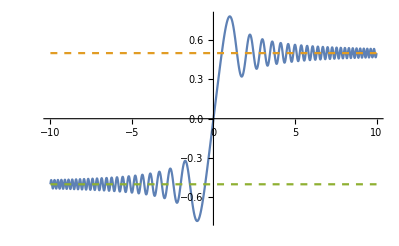

```mathematica
Plot[{FresnelC[x],1/2,-1/2},{x,-10,10},PlotStyle->{Automatic,Dashed,Dashed}]
```

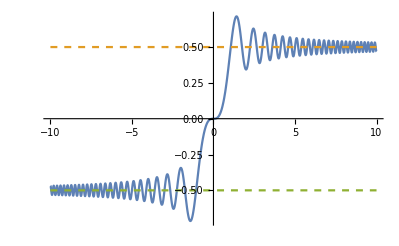

```mathematica
Plot[{FresnelS[x],1/2,-1/2},{x,-10,10},PlotStyle->{Automatic,Dashed,Dashed}]
```

```mathematica
S1[x_,m_]:=1/(π*x)*Sum[(-1)^(n+1)/((π*x^2)^(2n+1))*Product[2p+1,{p,2n}],{n,0,m}]
```

```mathematica
S2[x_,m_]:=1/(π*x)*Sum[(-1)^(n+1)/((π*x^2)^(2n))*Product[2p+1,{p,2n-1}],{n,0,m}]
```

```mathematica
Cx[x_,m_]:=1/2+S1[x,m]*Cos[π*x^2/2]-S2[x,m]*Sin[π*x^2/2]
```

```mathematica
Sx[x_,m_]:=1/2+S1[x,m]*Sin[π*x^2/2]+S2[x,m]*Cos[π*x^2/2]
```

```mathematica
Sx[5,3]
```

1/2+(27027/(1220703125 π^7)-189/(1953125 π^5)+3/(3125 π^3)-1/(25 π))/(5 π)

```mathematica
N[FresnelS[5]]
```

0.499191

```mathematica
NumberForm[0.49919138191711687,16]
```

0.4991913819171168

```mathematica
DiscretePlot[Sx[5,n],{n,1,75}]
```

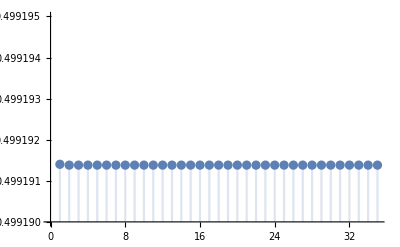

```mathematica
DiscretePlot[Sx[5,n],{n,1,35},PlotRange->{0.499190,0.499195}]
```

```mathematica
DiscretePlot[Cx[5,n],{n,1,75}]
```

# Integral Exponencial:

```mathematica
Plot[{ExpIntegralEi[x],Exp[x]},{x,1,10},PlotStyle->{Automatic,Dashed},PlotRange->{0,2500}]
```

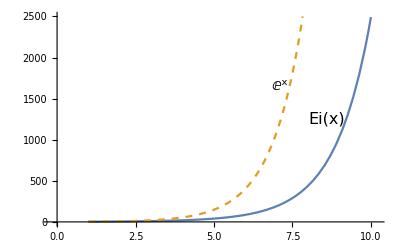

```mathematica
Ei[x_,j_]:=ⅇ^x*Sum[p!/(x^(p+1)),{p,0,j}]
```

```mathematica
N[ExpIntegralEi[10]]
```

2492.23

```mathematica
Abs[Ei[10,10]-N[ExpIntegralEi[10]]]
```

475.003

```mathematica
N[Ei[10,10]]
```

2493.29

```mathematica
Ei[10,10]
```

(3537353 ⅇ^10)/31250000

```mathematica
N[(3537353 ⅇ^10)/31250000]
```

2493.29

```mathematica
Abs[(ExpIntegralEi[10]-Ei[10,10])]/ExpIntegralEi[10]*100
```

(100 ((3537353 ⅇ^10)/31250000-ExpIntegralEi[10]))/ExpIntegralEi[10]

```mathematica
N[(100 (-(572387 ⅇ^10)/6250000+ExpIntegralEi[10]))/ExpIntegralEi[10]]
```

19.0594

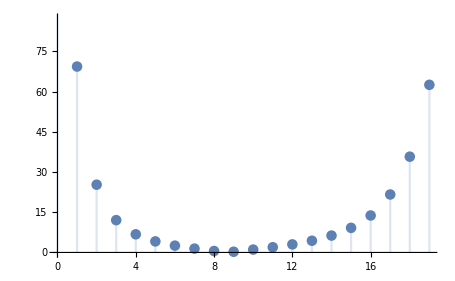

```mathematica
DiscretePlot[{Abs[Ei[10,n]-N[ExpIntegralEi[10]]]},{n,0,19}]
```

```mathematica
DiscretePlot[{Abs[N[ExpIntegralEi[10]]-Ei[10,n]]},{n,0,19}]
```

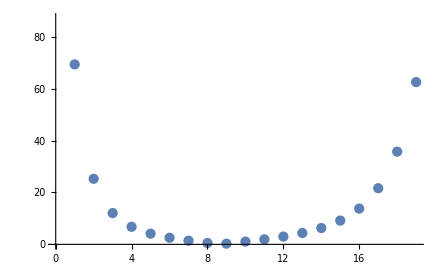

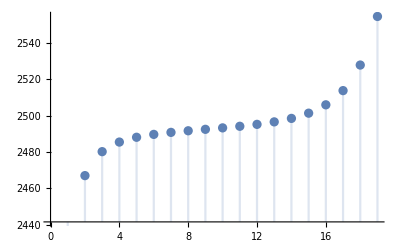

```mathematica
DiscretePlot[Ei[10,n],{n,0,19}]
```

```mathematica
Show[DiscretePlot[Ei[10,n],{n,0,19}],Plot[t=N[ExpIntegralEi[10]],{t,0,19}]]
```

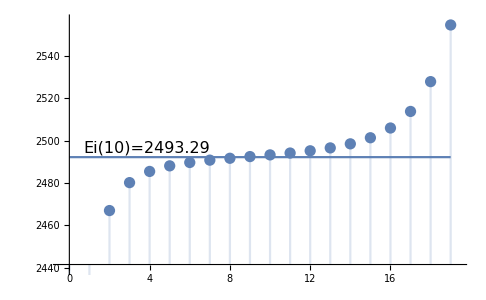

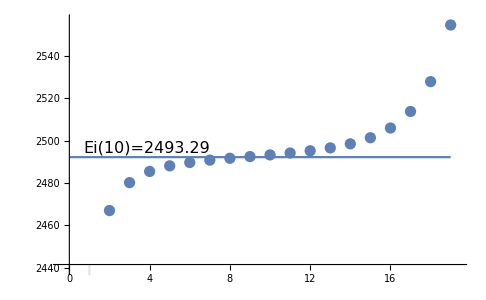

#### limite:

```mathematica
ⅇ^-u (-2-n) u^(-3-n)-ⅇ^-u u^(-2-n)
```

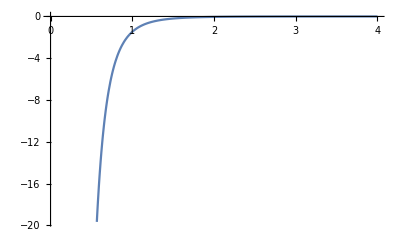

n=1

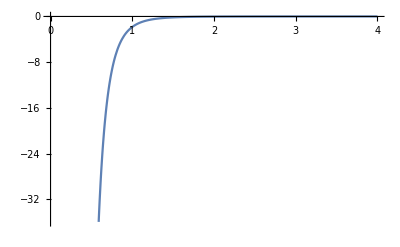

n=2

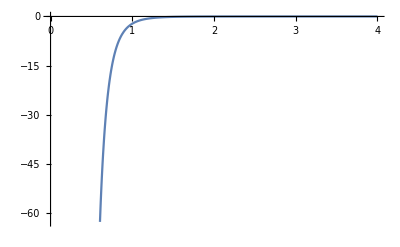

n=3

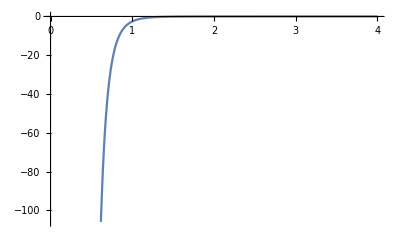

n=4

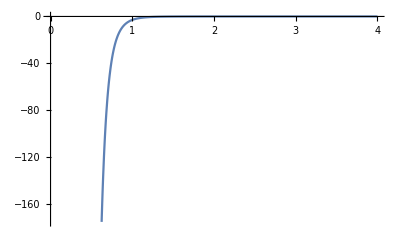

n=5

```mathematica
Do[a=Plot[ⅇ^-u (-2-n) u^(-3-n)-ⅇ^-u u^(-2-n),{u,0,4}];Print[a];Print["n=",n],{n,5}]
```

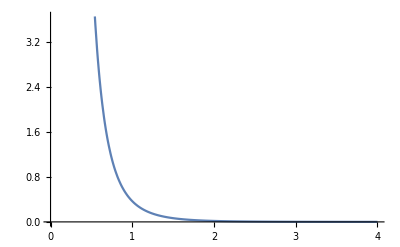

n=1

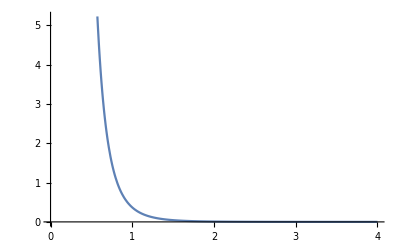

n=2

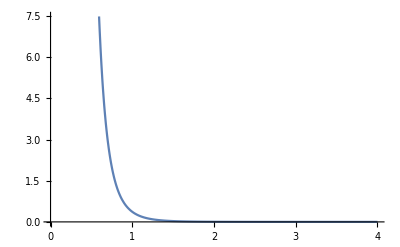

n=3

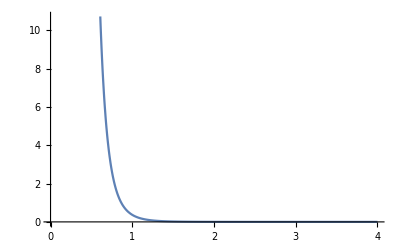

n=4

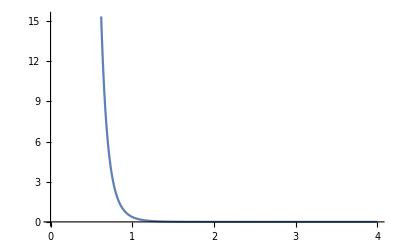

n=5

```mathematica
Do[a=Plot[ⅇ^(-u)/(u^(n+2)),{u,0,4}];Print[a];Print["n=",n],{n,5}]
```

```mathematica
D[ⅇ^(-u)/(u^(n+2)),u]
```

ⅇ^-u (-2-n) u^(-3-n)-ⅇ^-u u^(-2-n)

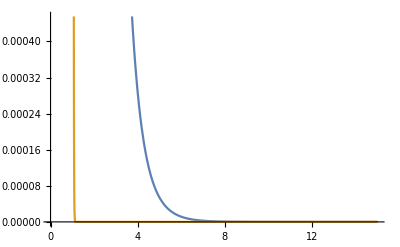

```mathematica
Plot[{ⅇ^(-u)/(u^3),ⅇ^(-u)/(u^100)},{u,0,15}]
```

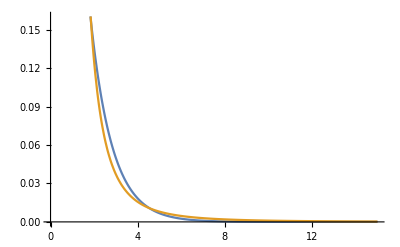

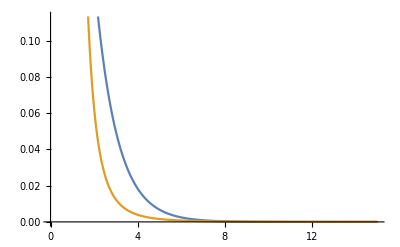

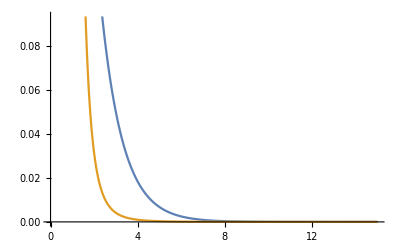

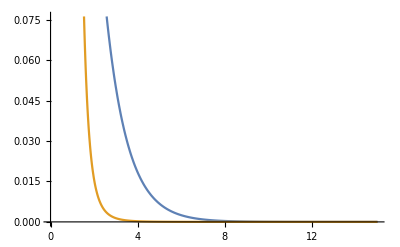

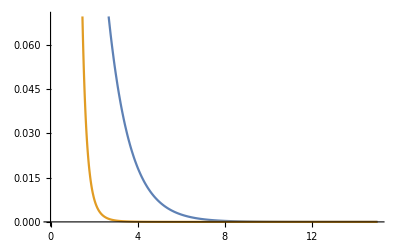

```mathematica
Do[a=Plot[{ⅇ^(-u),1/(u^(n+2))},{u,0,15}];Print[a],{n,5}]
```

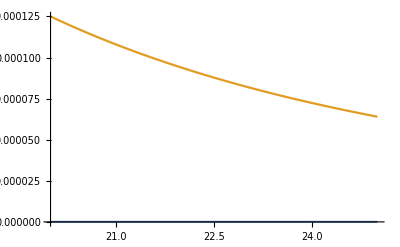

n=1

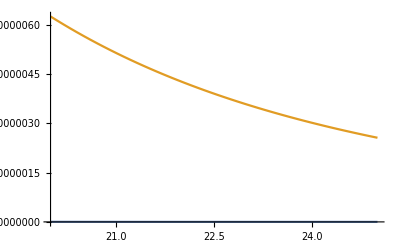

n=2

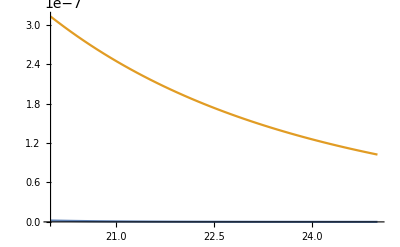

n=3

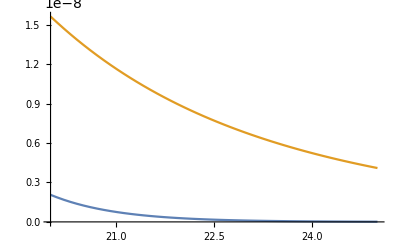

n=4

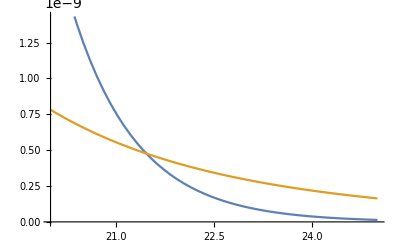

n=5

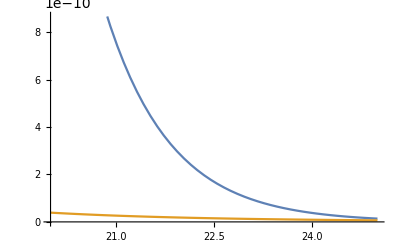

n=6

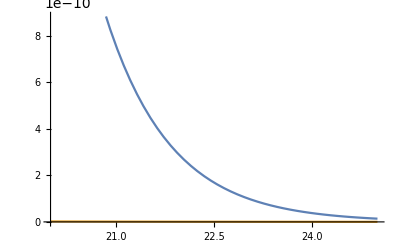

n=7

```mathematica
Do[a=Plot[{ⅇ^(-u),1/(u^(n+2))},{u,20,25}];Print[a];Print["n=",n],{n,7}]
```

# Função de Airy:

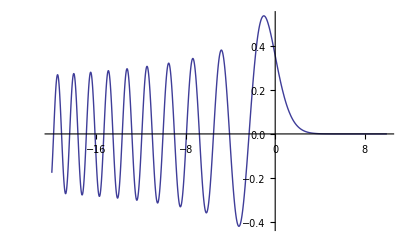

```mathematica
Plot[AiryAi[x],{x,-20,10}]
```

# Função Erro de Gauss:

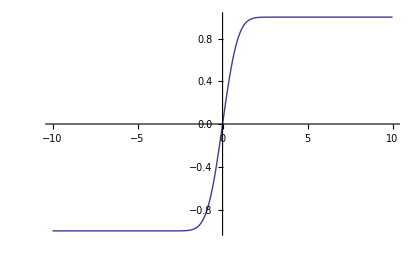

```mathematica
Plot[Erf[x],{x,-10,10}]
```

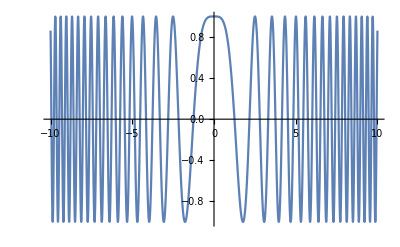

```mathematica
Plot[Cos[u^2],{u,-10,10}]
```

```mathematica
Sum[BernoulliB[n+2]/((n+2)n!)*t^n,{n,1,+∞}]
```

(12-t^2-3 t^2 Csch[t/2]^2)/(12 t^2)

```mathematica
Series[(12-t^2-3 t^2 Csch[t/2]^2)/(12 t^2),{t,0,3}]
```

-t^2/240+O[t]^4

```mathematica
BernoulliB[1]
```

-1/2

```mathematica
BernoulliB[2]
```

1/6

```mathematica
D[Coth[t/2],t]
```

-1/2 Csch[t/2]^2